## Goal

Given any input state, classify it into:

- dies out
- contains multiple solutions
- periodic without shift
- periodic with shift s
- aperiodic (e.g. glider gun)

The DetectPeriod[list] function, when given an initial state, returns an association with the period, canonical representation (i.e. smallest reachable state that gives that same solution), and shift.

## Implementation

### Rule Analysis

```mathematica
PointApplyRule[rule_,init_]:=CellularAutomaton[rule, init, 1][[2,(Length[init]+1)/2]]
```

```mathematica
AnalyzeRule[{n_, {k_, 1}, r_}]:=AnalyzeRule[{n, {k, 1}, r}]=Module[{rule={n, {k, 1}, r},minimumtolerablegap=2r+1},
While[AllTrue[Tuples[Range[k]-1, 2r+2-minimumtolerablegap], PointApplyRule[rule, PadLeft[#, 2r+1]]==0&], minimumtolerablegap--];
<|"Rule"->rule, "Colors"->k, "Totalistic"->True, "Radius"->r, "MinimumTolerableGap"->minimumtolerablegap|>
]
AnalyzeRule[{n_, k_, r_}]:=AnalyzeRule[{n, k, r}]=Module[{rule={n,k, r},minimumtolerablegap=2r+1},
While[AllTrue[Tuples[{0, 1}, 2r+2-minimumtolerablegap], PointApplyRule[rule, PadLeft[#, 2r+1]]==0&], minimumtolerablegap--];
<|"Rule"->rule, "Colors"->k, "Totalistic"->True, "Radius"->r, "MinimumTolerableGap"->minimumtolerablegap|>
]
AnalyzeRule[{n_, k_}]:=AnalyzeRule[{n, k, 1}]
AnalyzeRule[{n_}]:=AnalyzeRule[{n, 2}]
AnalyzeRule[n_]:=AnalyzeRule[{n}]

Timing[AnalyzeRule[{20, {2, 1}, 2}]]
AnalyzeRule[{2, {2, 1}, 2}]
AnalyzeRule[{32, {2, 1}, 2}]
AnalyzeRule[30]
RepeatedTiming[AnalyzeRule[{20, {2, 1}, 2}]]
```

{0.002462,<|Rule→{20,{2,1},2},Colors→2,Totalistic→True,Radius→2,MinimumTolerableGap→4|>}

<|Rule→{2,{2,1},2},Colors→2,Totalistic→True,Radius→2,MinimumTolerableGap→5|>

<|Rule→{32,{2,1},2},Colors→2,Totalistic→True,Radius→2,MinimumTolerableGap→1|>

<|Rule→{30,2,1},Colors→2,Totalistic→True,Radius→1,MinimumTolerableGap→3|>

{1.36376×10^-7,<|Rule→{20,{2,1},2},Colors→2,Totalistic→True,Radius→2,MinimumTolerableGap→4|>}

### Helper Functions

```mathematica
CloseKernels[];
LaunchKernels[];
```

```mathematica
Clear[AArrayPlot];
AArrayPlot[rule_, init_List, steps_:100, meshQ_:True]:=ArrayPlot[RunCA[rule, init, steps], Mesh->meshQ]
AArrayPlot[rule_,init_Integer, args___]:=AArrayPlot[rule, IntegerDigits[init, AnalyzeRule[rule]["Colors"]], args]

AArrayPlot[rule_][init_List, args___]:=AArrayPlot[rule, init, args]
AArrayPlot[rule_, args___][init_Integer]:=AArrayPlot[rule, init, args]
AArrayPlot[rule_][init_List, args___]:=AArrayPlot[rule, init, args]
AArrayPlot[rule_, args___][init_Integer]:=AArrayPlot[rule, init, args]
```

```mathematica
code20rule={20, {2, 1}, 2};
RunCA[rule_, init_, steps_]:=(mostrecentlyusedrule=rule;CellularAutomaton[rule, {init, 0}, steps])
RunCode20[init_, steps_]:=RunCA[code20rule, init, steps]
```

```mathematica
AllZeros=FunctionCompile[Function[Typed[list,"PackedArray"::["MachineInteger", 1]], Module[{i=Length[list]}, While[i>0&&list[[i]]==0, i--;]; i==0]], CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3], "AbortHandling"->False, "OptimizationLevel"->3,"InvocationMode"->"Standalone"}];
RepeatedTiming[AllZeros[{0, 0, 0, 0, 1, 0}]]
RepeatedTiming[Max[{0, 0, 0, 0, 1, 0}]==0]
```

{1.77231×10^-7,False}

{1.89881×10^-7,False}

```mathematica
StripZeros=FunctionCompile[Function[Typed[list, "PackedArray"::["MachineInteger", 1]],Module[
{i=1, j=Length[list]},
If[
(* AllZeros *)
Module[{i0=Length[list]}, While[i0>0&&list[[i0]]==0, i0--;]; i0==0],
 Return[Table[0, {iter, 0}]]
];
While[list[[i]]==0, i++];
 While[list[[j]]==0, j--]; 
list[[i;;j]]
]], CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3], "AbortHandling"->False, "OptimizationLevel"->3,"InvocationMode"->"Standalone"}];

RepeatedTiming[StripZeros[RandomInteger[{0, 1}, 1000]]]//First
StripZeros[{0, 0, 0, 0,0}]
```

1.5615×10^-6

{}

```mathematica
MaxGapLength=FunctionCompile[Function[Typed[list, "PackedArray"::["MachineInteger", 1]],Module[
{currentlen=0, maxlen=0},
Do[currentlen=If[i==0, currentlen+1,0]; 
maxlen=Max[maxlen, currentlen];, {i,list}];
maxlen
]], CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3], "AbortHandling"->False, "OptimizationLevel"->3,"InvocationMode"->"Standalone"}];
RepeatedTiming[MaxGapLength[RandomInteger[{0, 1}, 1000]]]
```

{4.72861×10^-6,9}

```mathematica
FindRepeatDeterministic[list_]:=
list[[-First[FirstPosition[Reverse[list[[;;-2]]], list[[-1]], {0}]];;]]
```

```mathematica
Clear[SplitSeparateSolutions];
SplitSeparateSolutions[carun_, mtg_]:=Module[{mask, mc, colors, carunpadded},
carunpadded=PadLeft[carun, {Length[carun], Length[carun[[-1]]]+mtg}];
mask=Sum[carunpadded[[All,i;;(i-mtg-1)]], {i, mtg}];
mc=Last[MorphologicalComponents[Image[mask], CornerNeighbors->False]];
colors=Union[mc];
Select[Table[(1-Unitize[c-mc[[2;;]]])*carun[[-1]], {c, colors}], Not@*AllZeros]
]

SplitSeparateSolutions[RunCode20[IntegerDigits[233 + 2^14 * 151, 2], 100], 4]
SplitSeparateSolutions[RunCode20[IntegerDigits[12555286547204781505564672, 2], 100], 4]
First@RepeatedTiming[SplitSeparateSolutions[RunCode20[IntegerDigits[12555286547204781505564672, 2], 100], 4]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,0,1},{1,0,0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{{1,0,0,1,1,0,0,0,0,1,0,1,1,0,1,1,0,0,0,1,0,1,0,0,1,0,0,1,0,0,1,0,0,0,1,1,1,1,1,0,0,1,1,1,1,1,1,0,0,0,1,1,1,1,1,1,0,0,1,0,1,1,0,1,1,1,1,0,1,1,1,1,0}}

0.00104033

### Detect Period

```mathematica
Clear[DetectPeriod];
DetectPeriod[rule_, n_Integer, args___]:=DetectPeriod[rule, IntegerDigits[n, AnalyzeRule[rule]["Colors"]], args]
DetectPeriod[rule_, list_List, steps_:200, maxdepth_:20]:=With[{ra=AnalyzeRule[rule]}, {res=DetectPeriodSub[ra, list, steps, maxdepth]},Join[<|"Rule"->rule,"Canonical"->FromDigits[list, ra["Colors"]], "Original"->FromDigits[list, ra["Colors"]], "MaxDepth"->maxdepth-#LowestDepth, "MaxSteps"->steps*(2^(1+maxdepth-#LowestDepth)-1)|>, #]&/@res];

DetectPeriodSub[ra_, list_, steps_, ogmaxdepth_]:=Module[
{carun, frd, separatesolutions, period, canonical, shift, maxdepth},
maxdepth=ogmaxdepth;

If[maxdepth<0,
Print["Something Went Wrong."];
];

carun=RunCA[ra["Rule"], list, steps];


If[ByteCount[carun]>800000, maxdepth=Min[maxdepth, 1]];

(* If it dies, return *);
If[AllZeros[carun[[-1]]], Return[{}]];

(* Detect Periodicity *)
frd=FindRepeatDeterministic[StripZeros/@carun];

If[maxdepth<=0,If[Length[frd]==0,
Return[{<|"Period"->0, "IsGliderGun"->True, "LowestDepth"->maxdepth|>}],
Return[{<|"Period"->Length[frd],"Canonical"->Min[Min[FromDigits[StripZeros[#],ra["Colors"]]&/@frd], Min[FromDigits[Reverse[StripZeros[#]],ra["Colors"]]&/@frd]], "IsUnfinished"->True, "LowestDepth"->maxdepth|>}];
]];

(* If unfinished and probably unseparated, recurse with more steps *);
If[Length[frd]==0, 
Return[If[MaxGapLength[carun[[-1]]]>15,
separatesolutions=SplitSeparateSolutions[carun, ra["MinimumTolerableGap"]];
Join@@Table[
DetectPeriodSub[ra, subsolution, steps, maxdepth-1],
 {subsolution, separatesolutions}
],
DetectPeriodSub[ra, carun[[-1]], 2 * steps, maxdepth - 1]
]]
];

(* Otherwise, run again for pure periodicity *)
carun=RunCA[ra["Rule"], carun[[-1]], steps];

(* If it's multiperiodic, split solutions *);
separatesolutions=SplitSeparateSolutions[carun[[-Length[frd];;]], ra["MinimumTolerableGap"]];
(*separatesolutions= SortBy[separatesolutions,First[FirstPosition[#, 1, 0]]&] *);

(* Recurse on each subsolution, if they exist *);
If[Length[separatesolutions]>1,
Return[Join@@Table[
DetectPeriodSub[ra, subsolution, steps, maxdepth-1],
 {subsolution, separatesolutions}
]]
];

(* Return single-solution period *);
period=Length[frd];
canonical=Min[Min[FromDigits[StripZeros[#],ra["Colors"]]&/@frd], Min[FromDigits[StripZeros[Reverse[#]],ra["Colors"]]&/@frd]];
carun=RunCA[ra["Rule"],IntegerDigits[canonical, ra["Colors"]], period];
shift=Log[ra["Colors"],FromDigits[First[carun], ra["Colors"]]/FromDigits[Last[carun], ra["Colors"]]];

Return[{<|"Period"->period,"Canonical"->canonical, "Shift"->shift, "LowestDepth"->maxdepth|>}];
]
```

```mathematica
DetectPeriod[{20, {2, 1}, 2},EchoFunction[AArrayPlot[code20rule]]@RandomInteger[1, 1000]]
```

-Graphics-

{<|Rule→{20,{2,1},2},Canonical→151,Original→5488429491527968487082071568804394482208923520395361687291569433526131695220220110536511893275426366534361615840895942197695378023641373218428782596128532143047860085638627631503255144258679696996054104307291982357017064373302482312202143616356565515898873087206587177404377887758375441698110398014693,MaxDepth→19,MaxSteps→125829000,Period→2,Shift→0,LowestDepth→1|>}

## Code 20 Testing

### Small-Scale Testing

```mathematica
list=;
DetectPeriod[code20rule, list]

list=;
DetectPeriod[code20rule, list]

list=;
DetectPeriod[code20rule, list]
```

{<|Rule→{20,{2,1},2},Canonical→151,Original→435283611217396771358931413484,Period→2,Shift→0|>,<|Rule→{20,{2,1},2},Canonical→151,Original→435283611217396771358931413484,Period→2,Shift→0|>}

{<|Rule→{20,{2,1},2},Canonical→360759087837221,Original→1943815430040652325859106676803873275904,Period→10,Shift→0|>,<|Rule→{20,{2,1},2},Canonical→360759087837221,Original→1943815430040652325859106676803873275904,Period→10,Shift→0|>}

{<|Rule→{20,{2,1},2},Canonical→360759087837221,Original→12105066281216059113659,Period→10,Shift→0|>,<|Rule→{20,{2,1},2},Canonical→187,Original→12105066281216059113659,Period→9,Shift→1|>}

```mathematica
foundsolutions=Normal[ResourceData["Persistent Structures in the Code 20 Cellular Automaton"]][[All, "Number"]]

d1=Table[First[DetectPeriod[code20rule, IntegerDigits[s, 2]]], {s, foundsolutions}][[All, "Period"]]
d2=Normal[ResourceData["Persistent Structures in the Code 20 Cellular Automaton"]][[All, "Period"]]
d1==d2

d1=Table[First[DetectPeriod[code20rule, IntegerDigits[s, 2]]], {s, foundsolutions}][[All, "Shift"]]
d2=Normal[ResourceData["Persistent Structures in the Code 20 Cellular Automaton"]][[All, "Shift"]]
Abs[d1]==Abs[d2]
```

{151,187,189,195,221,635,889,125231,595703,610999,14871103,16537415,256296063,22503642597,222678959859,10495070598767,360759087837221,2197520782601119,11221488970893447375,142082121178470981231}

{2,9,1,22,9,1,1,38,4,4,2,2,5,5,3,8,10,10,6,10}

{2,9,1,22,9,1,1,38,4,4,2,2,5,5,3,8,10,10,6,10}

True

{0,1,0,0,1,1,1,0,0,0,1,1,0,0,0,0,0,0,0,0}

{0,1,0,0,-1,1,-1,0,0,0,1,-1,0,0,0,0,0,0,0,0}

True

### Testing and Large Scale Search

```mathematica
list=;
ArrayPlot[RunCode20[list, 100]]
DetectPeriod[code20rule, list]//Column
```

-Graphics-

<|Rule→{20,{2,1},2},Canonical→151,Original→228213973957946518462231432912699579,Period→2,Shift→0|>
<|Rule→{20,{2,1},2},Canonical→151,Original→228213973957946518462231432912699579,Period→2,Shift→0|>
<|Rule→{20,{2,1},2},Canonical→187,Original→228213973957946518462231432912699579,Period→9,Shift→1|>

```mathematica
(* Find all solutions with periods that aren't easy to find *)
numtosearch=1000;
initwidth=100;
easysolutionperiods={0, 1, 2};  (* include 9 and 22, then 4 and 38 for longer searches *)


easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];

found=ParallelTable[If[AllTrue[DetectPeriod[code20rule, #, 50][[All, "Period"]], elem|->elem/.easysolutionperiods],Nothing,#]&[RandomInteger[{0, 1}, initwidth]], {i, numtosearch}][[;;UpTo[100]]];

ParallelTable[
Labeled[ArrayPlot[RunCode20[sol, 200]], ClickToCopy[Values@DetectPeriod[code20rule,sol], sol]],{sol, found}]
```

#### What is the best width and step size?

```mathematica
data=Join@@Table[(PrintTemporary[#]; #)&@{w, steps, 1/(First[Timing[l=Length[Join@@ParallelTable[DetectPeriod[code20rule, RandomInteger[{0, 1}, w], steps], {i, 100}]]]]/l)}, {w, {25, 50, 100, 250, 500, 1000, 2500, 5000, 10000}}, {steps, {20, 30, 40, 50,60, 70, 80, 90,100, 125,175, 250, 500}}];
```

```mathematica
SortBy[data, -#[[3]]&][[;;UpTo[20]]]
```

{{2500,50,2884.24},{2500,40,2758.53},{5000,50,2724.32},{5000,60,2603.2},{5000,40,2545.63},{2500,30,2464.25},{5000,70,2456.72},{5000,30,2371.86},{2500,60,2342.07},{5000,80,2312.55},{10000,70,2281.77},{2500,80,2277.94},{5000,90,2231.28},{2500,100,2129.79},{10000,50,2122.37},{2500,70,2105.42},{10000,60,2086.63},{1000,40,2070.32},{5000,100,2051.88},{2500,90,2014.95}}

```mathematica
ListPlot3D[data, Mesh->All]
```

-Graphics3D-

#### Large Solution Search:

```mathematica
(* Find all solutions with periods that aren't easy to find *)
numtosearch=100000;
initwidth=500;
easysolutionperiods={0, 1, 2, 4, 9, 22, 38};  (* include 9 and 22, then 4 and 38 for longer searches *)


easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];

found=ParallelTable[If[AllTrue[DetectPeriod[code20rule,#][[All, "Period"]], elem|->elem/.easysolutionperiods],Nothing,#]&[RandomInteger[{0, 1}, initwidth]], {i, numtosearch}];

ParallelTable[
Labeled[ArrayPlot[RunCode20[sol, 200]], ClickToCopy[Values@DetectPeriod[code20rule,sol], sol]],{sol, found[[;;UpTo[25]]]}]
```

$Aborted

$Aborted

```mathematica
found=Union[(Join@@ParallelTable[DetectPeriod[code20rule,IntegerDigits[2i+1, 2]], {i, 1000000}])[[All, "Canonical"]]]

ParallelTable[
Labeled[ArrayPlot[RunCode20[sol, 200]], ClickToCopy[Values@DetectPeriod[code20rule,sol], sol]],{sol, IntegerDigits[#, 2]&/@found[[;;UpTo[25]]]}]
```

{151,187,189,635,15903,125231,595703,610999}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Code 1329 Testing

```mathematica
code1329rule={1329,{3,1},1};
RunCode1329[init_, steps_]:=RunCA[code1329rule, init, steps]
IRunCode1329[n_, steps_]:=RunCode1329[IntegerDigits[n, 3], steps]
```

```mathematica
examples1329=Join[{2339825581, 1076975378,3192417282}, {54889,97439,166426}];
ClickToCopy[AArrayPlot[code1329rule, #, 300], #]&/@ examples1329
```

{-Graphics-2339825581,-Graphics-1076975378,-Graphics-3192417282,-Graphics-54889,-Graphics-97439,-Graphics-166426}

```mathematica
Labeled[AArrayPlot[code1329rule, #, 300],DetectPeriod[code1329rule, #]]&/@examples1329
```

```mathematica
results=DedupSame[Join@@ParallelTable[DedupSame[Join@@Table[Union[DetectPeriod[code20rule, RandomInteger[1, 100]]], {i, 100}]], {j, 10}]]
```

{<|Rule→{20,{2,1},2},Canonical→151,Original→17975262837708909884124502055,MaxDepth→0,MaxSteps→120,Period→2,Shift→0,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→187,Original→15057886442365993434746873268,MaxDepth→0,MaxSteps→120,Period→9,Shift→1,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→189,Original→75619847247795598610120896560,MaxDepth→0,MaxSteps→120,Period→1,Shift→0,LowestDepth→20|>,<|Rule→{20,{2,1},2},Canonical→15903,Original→108461267841564508145948647653,MaxDepth→0,MaxSteps→120,Period→22,Shift→0,LowestDepth→20|>}

## Testing Frameworks etc. for Batch Jobs

```mathematica
DedupSame[associations_, parameter_:"Canonical"]:=Union[associations,SameTest->(#1[parameter]==#2[parameter]&)]
```

```mathematica
VisualizeDetectPeriod[rule_, init_, stepsog_:None]:=Module[{results, steps},
results=DetectPeriod[code1329rule, init];
steps=If[stepsog===None, Min[1000, Max[results[[All, "MaxSteps"]]]], stepsog];

Row[{
ClickToCopy[AArrayPlot[code1329rule, init, steps, False], results],
Row[
ClickToCopy[Labeled[
AArrayPlot[code1329rule,#Canonical, 2*#Period/.(0->2*steps), #Period!=0]
, #Period/.(0->"None")], #Canonical]&
/@results
]
}]
]
MultiVisualizeDetectPeriod[rule_, inits_, args___]:=Column[ParallelTable[VisualizeDetectPeriod[rule, init, args], {init, inits}]]
```

```mathematica
MultiVisualizeDetectPeriod[code1329rule,examples1329]
```

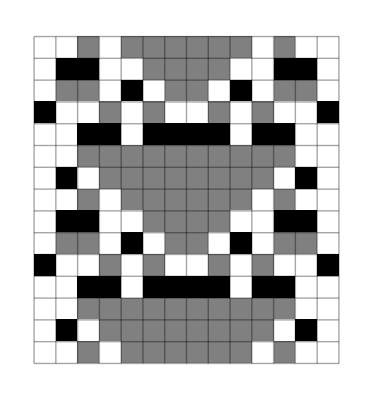
-Graphics-{<|Rule→{1329,{3,1},1},Canonical→9571,Original→2015147012679026553746602754814132375036274657,MaxDepth→6,MaxSteps→15240,Period→78,Shift→0,LowestDepth→14|>,<|Rule→{1329,{3,1},1},Canonical→9571,Original→2015147012679026553746602754814132375036274657,MaxDepth→6,MaxSteps→15240,Period→78,Shift→0,LowestDepth→14|>,<|Rule→{1329,{3,1},1},Canonical→9571,Original→2015147012679026553746602754814132375036274657,MaxDepth→3,MaxSteps→1800,Period→78,Shift→0,LowestDepth→17|>}-Graphics-9571-Graphics-9571-Graphics-9571
-Graphics-{<|Rule→{1329,{3,1},1},Canonical→22234,Original→282046425287958862784959640969647492885932033419,MaxDepth→2,MaxSteps→840,Period→12,Shift→0,LowestDepth→18|>,<|Rule→{1329,{3,1},1},Canonical→9571,Original→282046425287958862784959640969647492885932033419,MaxDepth→2,MaxSteps→840,Period→78,Shift→0,LowestDepth→18|>,<|Rule→{1329,{3,1},1},Canonical→9571,Original→282046425287958862784959640969647492885932033419,MaxDepth→2,MaxSteps→840,Period→78,Shift→0,LowestDepth→18|>}-Graphics-22234-Graphics-9571-Graphics-9571
-Graphics-{<|Rule→{1329,{3,1},1},Canonical→22960,Original→37918659891368262846414627012849221603376108316,MaxDepth→3,MaxSteps→1800,Period→7,Shift→0,LowestDepth→17|>,<|Rule→{1329,{3,1},1},Canonical→9571,Original→37918659891368262846414627012849221603376108316,MaxDepth→3,MaxSteps→1800,Period→78,Shift→0,LowestDepth→17|>,<|Rule→{1329,{3,1},1},Canonical→9571,Original→37918659891368262846414627012849221603376108316,MaxDepth→2,MaxSteps→840,Period→78,Shift→0,LowestDepth→18|>}-Graphics-22960-Graphics-9571-Graphics-9571
-Graphics-{<|Rule→{1329,{3,1},1},Canonical→957100817674,Original→150042478570786251073985105364336836734500997395,MaxDepth→2,MaxSteps→840,Period→84,Shift→0,LowestDepth→18|>}-Graphics-957100817674
-Graphics-{<|Rule→{1329,{3,1},1},Canonical→1169069994691541,Original→417729995541957626998938738879678211055384210023,MaxDepth→3,MaxSteps→1800,Period→78,Shift→0,LowestDepth→17|>}-Graphics-1169069994691541
-Graphics-{<|Rule→{1329,{3,1},1},Canonical→525304562024518979,Original→37279264339387159915935443648681390999359463809,MaxDepth→6,MaxSteps→15240,Period→48,Shift→24,LowestDepth→14|>,<|Rule→{1329,{3,1},1},Canonical→9571,Original→37279264339387159915935443648681390999359463809,MaxDepth→7,MaxSteps→30600,Period→78,Shift→0,LowestDepth→13|>,<|Rule→{1329,{3,1},1},Canonical→9571,Original→37279264339387159915935443648681390999359463809,MaxDepth→4,MaxSteps→3720,Period→78,Shift→0,LowestDepth→16|>,<|Rule→{1329,{3,1},1},Canonical→9571,Original→37279264339387159915935443648681390999359463809,MaxDepth→4,MaxSteps→3720,Period→78,Shift→0,LowestDepth→16|>,<|Rule→{1329,{3,1},1},Canonical→9571,Original→37279264339387159915935443648681390999359463809,MaxDepth→6,MaxSteps→15240,Period→78,Shift→0,LowestDepth→14|>,<|Rule→{1329,{3,1},1},Canonical→9571,Original→37279264339387159915935443648681390999359463809,MaxDepth→6,MaxSteps→15240,Period→78,Shift→0,LowestDepth→14|>,<|Rule→{1329,{3,1},1},Canonical→9571,Original→37279264339387159915935443648681390999359463809,MaxDepth→4,MaxSteps→3720,Period→78,Shift→0,LowestDepth→16|>,<|Rule→{1329,{3,1},1},Canonical→9571,Original→37279264339387159915935443648681390999359463809,MaxDepth→3,MaxSteps→1800,Period→78,Shift→0,LowestDepth→17|>,<|Rule→{1329,{3,1},1},Canonical→9571,Original→37279264339387159915935443648681390999359463809,MaxDepth→4,MaxSteps→3720,Period→78,Shift→0,LowestDepth→16|>}-Graphics-525304562024518979-Graphics-9571-Graphics-9571-Graphics-9571-Graphics-9571-Graphics-9571-Graphics-9571-Graphics-9571-Graphics-9571

```mathematica
MultiVisualizeDetectPeriod[code1329rule, DedupSame[Join@@Table[DetectPeriod[code1329rule, RandomInteger[2, 100]], {i, 100}]][[All, "Original"]]]
```

```mathematica
{<|"Rule"->{1329,{3,1},1},"Canonical"->1169069994691541,"Original"->417729995541957626998938738879678211055384210023,"MaxDepth"->3,"MaxSteps"->1800,"Period"->78,"Shift"->0,"LowestDepth"->17|>}
```

```mathematica
AArrayPlot[code1329rule,957100817674, 500]
```

-Graphics-

### Batch Jobs

```mathematica
numberOfBatches=50;
totalInitsToSearch=10000;
initWidth=100;
rule=code1329rule;

initsPerBatch = Round[totalInitsToSearch/numberOfBatches];
colors=AnalyzeRule[rule]["Colors"]
```

3

```mathematica
rawresults=ParallelTable[

DedupSame[Join@@Table[Union[DetectPeriod[rule, RandomInteger[{0,colors-1}, initWidth]]],{i, initsPerBatch}]]

, {j, numberOfBatches}];
```

$Aborted

```mathematica
results=DedupSame[Join@@rawresults];
Length[results]
MultiVisualizeDetectPeriod[rule, results[[;;UpTo[20], "Original"]]]
MultiVisualizeDetectPeriod[rule, Select[results, #Period==0&][[;;UpTo[20], "Original"]]]
```

201

$Aborted

```mathematica
AArrayPlot[code1329rule, 15416340273823942535580279585347100530421847372, 1200]
```

-Graphics-

```mathematica
AArrayPlot[code1329rule,80056569856531,200]
```

-Graphics-

```mathematica
AArrayPlot[code1329rule,83378670194990058536098217970956197035160380719, 1000]
```

-Graphics-

```mathematica
DetectPeriod[{1772277832,2,2}, 3637115]
```

{<|Rule→{1772277832,2,2},Canonical→223,Original→3637115,MaxDepth→20,MaxSteps→419430200,Period→3,IsUnfinished→True,LowestDepth→0|>,<|Rule→{1772277832,2,2},Canonical→223,Original→3637115,MaxDepth→20,MaxSteps→419430200,Period→3,IsUnfinished→True,LowestDepth→0|>,<|Rule→{1772277832,2,2},Canonical→223,Original→3637115,MaxDepth→20,MaxSteps→419430200,Period→3,IsUnfinished→True,LowestDepth→0|>}